```mathematica
data={};
For[i=1,i≤118,i++,
data=Append[data,Transpose[{IsotopeData[i,"NeutronNumber"],IsotopeData[i,"AtomicNumber"],IsotopeData[i,"BindingEnergy"][[;;,1]]}]]
]
data=Flatten[data,1];
```

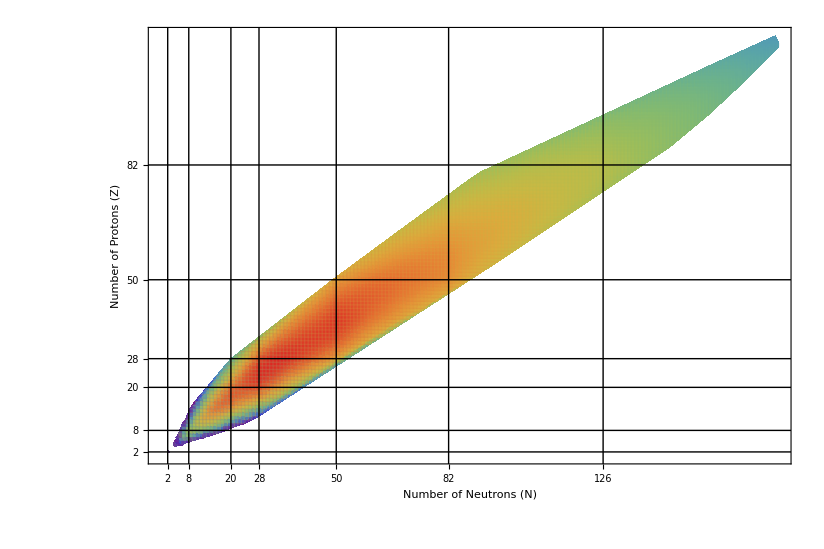

```mathematica
p=ListDensityPlot[data,
ColorFunction->"Rainbow",
Mesh->{Range[500],Range[118]},
Epilog->{
(*Add vertical lines*)
InfiniteLine[{2,0},{0,1}],
InfiniteLine[{8,0},{0,1}],
InfiniteLine[{20,0},{0,1}],
InfiniteLine[{28,0},{0,1}],
InfiniteLine[{50,0},{0,1}],
InfiniteLine[{82,0},{0,1}],
InfiniteLine[{126,0},{0,1}],
(*Add horizontal lines*)
InfiniteLine[{0,2},{1,0}],
InfiniteLine[{0,8},{1,0}],
InfiniteLine[{0,20},{1,0}],
InfiniteLine[{0,28},{1,0}],
InfiniteLine[{0,50},{1,0}],
InfiniteLine[{0,82},{1,0}]},
FrameLabel->{"Number of Neutrons (N)","Number of Protons (Z)"},
FrameStyle->18,
FrameTicks->{{2,8,20,28,50,82,126},{2,8,20,28,50,82},{},{}},
AspectRatio->118/177
]
```

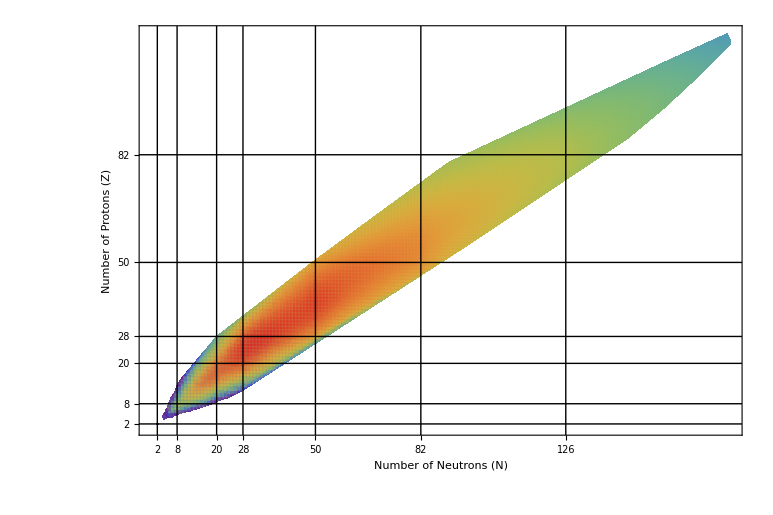

```mathematica
SetDirectory[NotebookDirectory[]]
(*Export["tableofnuclides.pdf",p,ImageResolution->5000]*)
(*Export["tableofnuclides.pdf",p]*)
```

/home/clpetrie/mygit/nuclear/work/dissertation/figures

```mathematica
Transpose[data][[1]]//Max
Transpose[data][[2]]//Max
```

177

118